#### Preamble

```mathematica
ClearAll @@ {$Context<>"*"}
```

```mathematica
SetDirectory[NotebookDirectory[]];
saveTask = CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]], 15 * 60];
StartScheduledTask[saveTask](*Saves nb each 15 minutes*);

<<"MaTeX`"
```

```mathematica
ColorMapSuitePath = "~/Documentos/Wolfram Mathematica/ScientificColourMaps8"
(* Function for continuous data *)
ColorMapSuite[name_String] := ColorMapSuite[name, -1]
ColorMapSuite[name_String, el_] := With[{
    list = Transpose@{Subdivide[0, 1, 255],
    RGBColor @@@ First@Import[ColorMapSuitePath <> "/" <> name <> "/" <> name <> ".mat"]}},
        Blend[list, {##}[[el]]] & ]
(* Colors for unordered data *)
ColorMapSuiteCategorical[name_String] :=  RGBColor @@@ First@Import[
            ColorMapSuitePath <> "/" <> name <> "/"<> "CategoricalPalettes"<> "/" <> name <> "S.mat"]
(* Colors for unordered data *)
ColorMapSuiteDiscrete[name_String] := ColorMapSuiteDiscrete[name,10]  
ColorMapSuiteDiscrete[name_String, num_Integer] :=  RGBColor @@@ First@Import[
            ColorMapSuitePath <> "/" <> name <> "/"<> "DiscretePalettes"<> "/" <> name <> ToString[num] <>".mat"]
```

~/Documentos/Wolfram Mathematica/ScientificColourMaps8

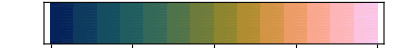

{RGBColor[0.005193153367084745, 0.0982381170217676, 0.3498418809830899],RGBColor[0.9813535753006561, 0.8004061671470218, 0.9812666660455576],RGBColor[0.5112531863663102, 0.5108978758437912, 0.19329557161683117],RGBColor[0.13329781036453003, 0.3752817757604749, 0.3793954095265211],RGBColor[0.9466116954773739, 0.6142184936872118, 0.4197671190995584],RGBColor[0.06689896495473623, 0.26318767055475906, 0.37759435604864444],RGBColor[0.9928996757060824, 0.7048518670395225, 0.7041140144806634],RGBColor[0.3023785627690957, 0.4502815737212346, 0.30012236213619936],RGBColor[0.7542682881292884, 0.5650332333700621, 0.211760789638594],RGBColor[0.4029676055462818, 0.48046597848254047, 0.24473116161388492],RGBColor[0.9890892793449574, 0.7509682178760204, 0.8379786653074179],RGBColor[0.6315126979581867, 0.540752449196533, 0.17007475185076026],RGBColor[0.9875668406547834, 0.6584217185210594, 0.5662264160947723],RGBColor[0.2090752388963242, 0.417412080725871, 0.3496767296453781],RGBColor[0.04937771055294349, 0.19107609466670547, 0.3658097737930779],RGBColor[0.08835319612192202, 0.32216699518938113, 0.3847307176551048],RGBColor[0.858747197113258, 0.5844403255814892, 0.2955720385448463],RGBColor[0.9734236573646047, 0.6351829029011401, 0.49254690556271924],RGBColor[0.1679516304435099, 0.3978894758325473, 0.36778403427924616],RGBColor[0.5700155866011719, 0.526185875241075, 0.17527272145547185],RGBColor[0.3519760378874838, 0.46544005687368395, 0.27249229457065943],RGBColor[0.1068415417894461, 0.3497740690589232, 0.38454754507201544],RGBColor[0.9913665497308912, 0.7276136928455845, 0.7702698492305938],RGBColor[0.6937199105780304, 0.5537967644647263, 0.18261027740926],RGBColor[0.03205278397327522, 0.14677416313591207, 0.3582388098645774],RGBColor[0.07583316231246431, 0.29332080890607, 0.3819221265171391],RGBColor[0.25445231948078745, 0.43452908459242406, 0.32643417320075546],RGBColor[0.9072416855607618, 0.5973189263808381, 0.35314225470189153],RGBColor[0.05916444726331392, 0.22984235549248522, 0.372251954677445],RGBColor[0.9859802453546757, 0.7752724373756446, 0.908448239797334],RGBColor[0.9925948391586693, 0.6819138828242806, 0.6368692956942783],RGBColor[0.4557739000068354, 0.4955846774693378, 0.2177743551480794],RGBColor[0.8116922177076217, 0.5751866844364272, 0.2525717360585131],RGBColor[0.6626912095384206, 0.5475028509940739, 0.1740441636457403],RGBColor[0.9876715115468123, 0.7629956264742592, 0.8728641334807893],RGBColor[0.18788592197876566, 0.4080032201407193, 0.35948448768180946],RGBColor[0.9922583962864815, 0.7162098672692777, 0.7371455146895275],RGBColor[0.0199356188871784, 0.12298460990134438, 0.354119746868454],RGBColor[0.4290943832351661, 0.48801065150519185, 0.23109635675825485],RGBColor[0.07111497011170888, 0.2784970788777719, 0.3798949405899265],RGBColor[0.23136234768511588, 0.4261974566798758, 0.3385720498359743],RGBColor[0.08155250132784678, 0.307858398947125, 0.38359755116259286],RGBColor[0.783415838135567, 0.570161596146816, 0.23096169818099238],RGBColor[0.8838779664462431, 0.5904499325689858, 0.32319477087540505],RGBColor[0.278171063633642, 0.44252433547295505, 0.3135517021145336],RGBColor[0.05472081902680487, 0.2112336395043889, 0.36918391837772296],RGBColor[0.042104481436739956, 0.16955702528601388, 0.3621513500244556],RGBColor[0.06307118851928215, 0.2470851847296836, 0.3750497628325021],RGBColor[0.11899185226757944, 0.36284860147640574, 0.38271289196822167],RGBColor[0.09661809539832363, 0.3361614658561598, 0.3851338100463711],RGBColor[0.9839125936007757, 0.787756858655277, 0.9446261751501791],RGBColor[0.9819179053428766, 0.6466637495214104, 0.5296023025308836],RGBColor[0.990925532131, 0.6702301975007446, 0.6020305430034925],RGBColor[0.14970605921174326, 0.3869750464356994, 0.37444878673936705],RGBColor[0.37729103199175273, 0.47295177298973484, 0.25858753735262613],RGBColor[0.5402253388010938, 0.5185841721042183, 0.183099222034565],RGBColor[0.9903065510455036, 0.7391843624833386, 0.8038097534534149],RGBColor[0.9931105441159147, 0.6934513233405696, 0.6708104867091674],RGBColor[0.9616963227638149, 0.6242822966856691, 0.45570178224399416],RGBColor[0.48312282972791437, 0.5032161985929168, 0.2050370497105667],RGBColor[0.6005204120803953, 0.5336045490746475, 0.1706478010371041],RGBColor[0.9283232091535554, 0.6052123838148247, 0.3854044343356354],RGBColor[0.32700657046640985, 0.45790041408363436, 0.28637653338724006],RGBColor[0.7243222900273982, 0.5596276419797932, 0.195408149901273],RGBColor[0.8322721663406366, 0.5790257300386646, 0.27021114257162154],RGBColor[0.9780522878867093, 0.6408681647557488, 0.511089790326883],RGBColor[0.9930743221588754, 0.6991606001856622, 0.6875192645539461],RGBColor[0.9545735519415848, 0.6191372742405447, 0.43758222343689757],RGBColor[0.3645890255190674, 0.4692131045104409, 0.2655434834600164],RGBColor[0.22011194218117586, 0.4218641753656316, 0.3442611096338137],RGBColor[0.04590454177718842, 0.18045998148098763, 0.36400713889938585],RGBColor[0.9894964040732597, 0.664328686022486, 0.5842462268216205],RGBColor[0.06105185290468469, 0.23862497540933905, 0.3736914837038787],RGBColor[0.012963349842328881, 0.11077922487868916, 0.3519924367491822],RGBColor[0.1586196382745385, 0.39253083557636365, 0.3713202601014282],RGBColor[0.9884064969216979, 0.7569487779511263, 0.8553321380307732],RGBColor[0.7976654656247937, 0.572681501867017, 0.24149026342353114],RGBColor[0.314648370646325, 0.45410714049204104, 0.29327876318162127],RGBColor[0.9929674063249064, 0.6877053160266439, 0.6539344520718204],RGBColor[0.7689417224250781, 0.5676303553824138, 0.22104513938190246],RGBColor[0.6470984735516427, 0.544182954477616, 0.17146485486178015],RGBColor[0.3900701662780218, 0.47671078250738447, 0.2516645567489511],RGBColor[0.9850020679635899, 0.781495470778951, 0.9264677968127821],RGBColor[0.9850658742908114, 0.6525215673894564, 0.5479984637725441],RGBColor[0.02629125326861058, 0.13504437659330928, 0.35621017793577603],RGBColor[0.0785169378778106, 0.30062163288111604, 0.3828141416419706],RGBColor[0.4693681759290078, 0.49939268549601173, 0.2113176200553523],RGBColor[0.5851991583363613, 0.529926872028961, 0.17249347219852024],RGBColor[0.14125972272499474, 0.3812395532769262, 0.37713457767678255],RGBColor[0.41596738524987337, 0.4842252855409939, 0.23789477741620474],RGBColor[0.29021386560947077, 0.44642003736878627, 0.3068891773422693],RGBColor[0.07344021874372691, 0.2859415755335133, 0.38095684875304925],RGBColor[0.9868679281152041, 0.7691045891720196, 0.8905725851461087],RGBColor[0.2427949464944569, 0.43041813391463224, 0.3326345960882581],RGBColor[0.991935238397665, 0.6760909921006679, 0.6195754855710046],RGBColor[0.05216442261319991, 0.2013231093466841, 0.36752442884120756],RGBColor[0.4423653391272914, 0.49179535392211904, 0.22435367889204286],RGBColor[0.06493599599964549, 0.2552641171581149, 0.3763622349015682],RGBColor[0.19830954704068637, 0.41279752713983114, 0.35476654101062277],RGBColor[0.9897201605469811, 0.7450391977175737, 0.8208041269437343]}

{RGBColor[0.005193153367084745, 0.0982381170217676, 0.3498418809830899],RGBColor[0.06307118851928215, 0.2470851847296836, 0.3750497628325021],RGBColor[0.10969518137400697, 0.3530981978863, 0.3842172172502675],RGBColor[0.23707454607405365, 0.42832460818730694, 0.33563448126966455],RGBColor[0.40945476550362553, 0.48235070950586556, 0.2413137980167112],RGBColor[0.6159723223277639, 0.537231237632357, 0.16982607466873542],RGBColor[0.8254723451653395, 0.5777251816245221, 0.26419650676207984],RGBColor[0.9708041934518005, 0.6323937061133272, 0.4832897189513224],RGBColor[0.9922583962864815, 0.7162098672692777, 0.7371455146895275],RGBColor[0.9813535753006561, 0.8004061671470218, 0.9812666660455576]}

```mathematica
DensityPlot[x,{x,0,1},{y,0,1},ColorFunction->ColorMapSuite["batlow"],AspectRatio->1/15, FrameTicks->{Automatic,None}]
ColorMapSuiteCategorical["batlow"]
ColorMapSuiteDiscrete["batlow"]
```

```mathematica
fs = 11;
texStyle := {FontFamily -> "Latin Modern Roman", FontSize -> fs, Black}
colors = ColorMapSuiteCategorical["batlow"];
(* Estilo por default de las gráficas *)
graphsOpts:={Mesh->None,
            BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->350,
             PlotStyle->Table[Directive[AbsoluteThickness[1.5],colors[[i]]],{i,Length[colors]}],Axes->False}
(* Estilo por default de las gráficas *)
STex:=Style[#,texStyle]&
MTex:=MaTeX[#,ContentPadding->False,FontSize->fs,"Preamble"->{"\\usepackage{color}"}]&
MTexU:=MaTeX[ # <> "\\,\\text{ [" <> #2 <> "]}",ContentPadding->False,FontSize->fs,"Preamble"->{"\\usepackage{color}"}]&
```

## Ecuación de Laplace

#### Analítico

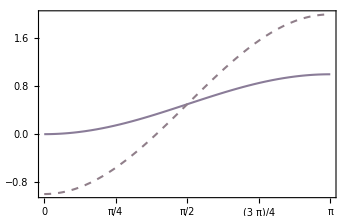

```mathematica
k = 1.; rad = 1; eps =1;

phiR[theta_]:= k*Sin[theta/2]^2
sigma[theta_]:= 0.5*(k*eps/rad)*(1-3.*Cos[theta])
 ft = {{Automatic, Automatic},
       {Join[Table[{i,i,.015},{i,Range[0, π, π/4]}],Table[{i,None,.01},{i,Range[0, π, π/40]}]], Automatic} };

plots = Show[{      
Plot[phiR[x],{x,0,Pi},
          ColorFunction->ColorMapSuite["batlow",1],
          Evaluate[graphsOpts], 
          FrameLabel->{{MTexU["\\text{--- }\\phi(r=R, \\theta)","$k$"],MTexU["---\\;\\sigma(\\theta)","$\\varepsilon_0 k/R$"]},
                      {MTexU["\\theta","deg"],None}},
      FrameTicks->ft ],
Plot[sigma[x],{x,0,Pi},
          ColorFunctionScaling->False,
          PlotStyle->Directive[AbsoluteThickness[1.5],Dashed],
           ColorFunction -> Function[{x, y}, ColorMapSuite["berlin",1][(y+2)/4]],
           Evaluate[graphsOpts]]
      },PlotRange->Full]
```

```mathematica
boundary = {0,0};
 boundary[[1]]= ParametricPlot[{Sin[v],Cos[v]},{v,-Pi,Pi},PlotStyle->AbsoluteThickness[15],
                Axes->False,PlotRange->1.25,
                ColorFunctionScaling->False,
                ImageSize->80,
                ColorFunction->Function[{x,y,v},ColorMapSuite["batlow"][phiR[v]]]]
                
boundary[[2]] = ParametricPlot[{Sin[v],Cos[v]},{v,-Pi,Pi},PlotStyle->AbsoluteThickness[15],
                Axes->False,PlotRange->1.25,ImageSize->80,
                ColorFunctionScaling->False,
                ColorFunction->Function[{x,y,v},ColorMapSuite["berlin"][(2+sigma[v])/4]]]
```

-Graphics-

-Graphics-

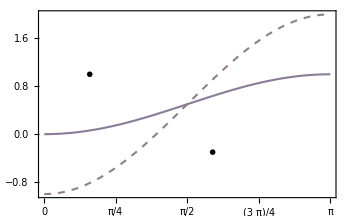

```mathematica
Show[plots,
Epilog->{Inset[boundary[[1]],{.5,1}],Inset[boundary[[2]],{1.85,-.3}]}]
```

Visualization`Core`DensityPlot::exclul: {√(Abs[y]^2+Abs[z]^2)-0,√(Abs[y]^2+Abs[z]^2)-0,Max[-False+(√(Power[«2»]+Power[«2»])≤1),-True+(√(Power[«2»]+Power[«2»])≤1)]-0,(-True+(√(Abs[«1»]^2+Abs[«1»]^2)≤1))-0} must be a list of equalities or real-valued functions.

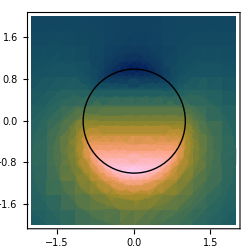

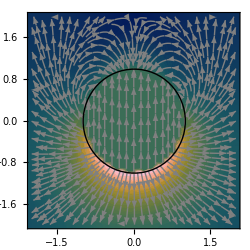

```mathematica
phi[y_,z_]:= Switch[Norm[{y,z}]<= rad, 
                        True, .5*k*(1-z/rad),
                        False, .5*k( # - (z /rad) * #^3 )&[rad/Norm[{y,z}]] ]
                        
eField[y_,z_]:= Module[{ez = {0,1},er,etheta, r = Norm[{y,z}]},
                    er = {y,z}/r;
                    etheta = {z,-y}/r; 
                  Switch[r<= rad, 
                        True, .5*k*ez/rad,
                        False, (.5*k/rad)*( er*( #- 2 * #^2 * (z/r))- etheta * ( #^2 * (y/r) ))&[rad/r]  ]                     
                     ]
DensityPlot[phi[y,z],{y,-2,2},{z,-2,2},
          Epilog->{Circle[]},
          MeshFunctions->{#3&},
          Mesh->10,
          FrameLabel->{MTexU["y","$R$"],MTexU["z","$R$"]},
          MeshStyle->Directive[Gray,Opacity[.5]],
          ColorFunction->ColorMapSuite["batlow"],
          PlotLegends->BarLegend[Automatic,LegendMarkerSize->220,LabelStyle->texStyle,LegendLabel->MTexU["\\phi(\\mathbf{r})","$k$"]],
          ImageSize->250,
          Evaluate[graphsOpts]]
          
StreamDensityPlot[eField[y,z],{y,-2,2},{z,-2,2},
    StreamPoints->Fine,
    Epilog->{Circle[]}, 
     Mesh->10,
     MeshStyle->Directive[Gray,Opacity[.5]],
      FrameLabel->{MTexU["y","$R$"],MTexU["z","$R$"]},
     ColorFunction->ColorMapSuite["batlow"],
     StreamColorFunction->Function[{x,y,z},Gray],
     PlotLegends->BarLegend[{ColorMapSuite["batlow"],{0,1.5}},LegendMarkerSize->220,LabelStyle->texStyle,LegendLabel->MTexU["||\mathbf{E}(\\mathbf{r})||","$\\frac{k}{R}$"]],
      BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->250]
```

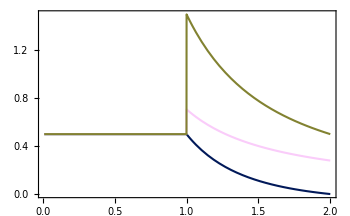

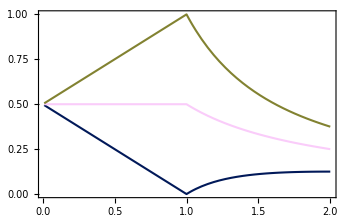

```mathematica
Plot[{Norm[eField[0,z]],Norm[eField[z,0]],Norm[eField[0,-z]]},{z,.01,2},
    PlotRange->All,
    PlotLegends-> Placed[SwatchLegend[Automatic, Map[MaTeX,{0,π/2,π}],LegendLabel->MTexU["\\theta","deg"]],{Left,Top}],
   FrameLabel->{MTexU["r","$R$"],MTexU["||\\mathbf{E}(\\mathbf{r})||","$k/R$"]},
    Evaluate[graphsOpts]]
    
Plot[{phi[0,z],phi[z,0],phi[0,-z]},{z,.01,2},
    PlotRange->All,
    PlotLegends-> Placed[SwatchLegend[Automatic, Map[MaTeX,{0,π/2,π}],LegendLabel->MTexU["\\theta","deg"]],{Right,Top}],
   FrameLabel->{MTexU["r","$R$"],MTexU["\\phi(\\mathbf{r})","$k$"]},
    Evaluate[graphsOpts]]
```